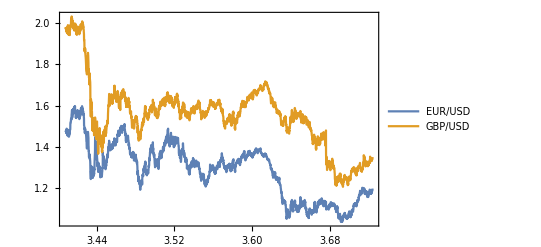

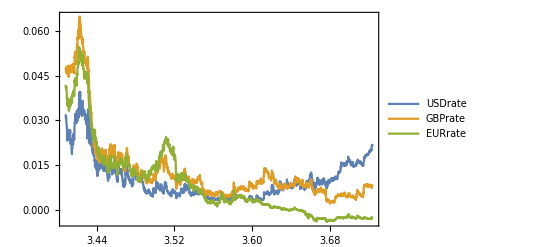

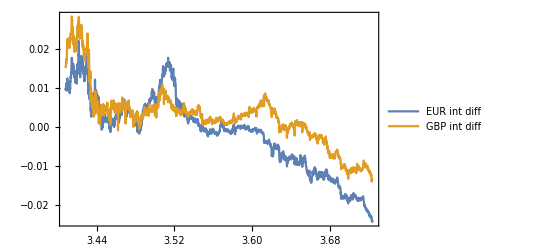

```mathematica
EURUSD=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,5}}];
eurusd=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],5}];
GBPUSD=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,6}}];
gbpusd=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],6}];
USDrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,4}}];
usdrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],4}];
GBPrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,3}}];
gbprate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],3}];
EURrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,2}}];
eurrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],2}];
date=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],1}];
gbpdiff=gbprate-usdrate;
eurdiff=eurrate-usdrate;
GBPdiff=Table[{date[[i]],gbpdiff[[i]]},{i,1,2477}];
EURdiff=Table[{date[[i]],eurdiff[[i]]},{i,1,2477}];
DateListPlot[{EURUSD,GBPUSD},PlotLegends->Placed[{"EUR/USD","GBP/USD"},Above]]
DateListPlot[{USDrate,GBPrate,EURrate},PlotRange->All,PlotLegends->Placed[{"USDrate","GBPrate","EURrate"},Above]]
DateListPlot[{EURdiff,GBPdiff},PlotLegends->Placed[{"EUR int diff","GBP int diff"},Above]]
```

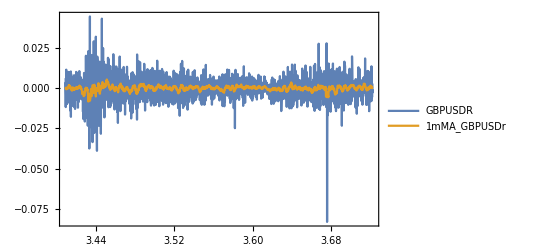

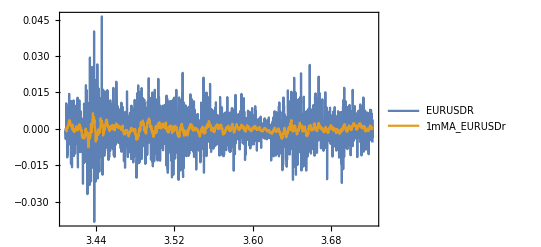

```mathematica
(*Detrended log return*)
gbpusdr=Differences[Log[gbpusd]];
eurusdr=Differences[Log[eurusd]];
GBPUSDr=Table[{date[[i+10]],gbpusdr[[i+10]]},{i,1,2455}];EURUSDr=Table[{date[[i+10]],eurusdr[[i+10]]},{i,1,2455}];
mMAgbpusdr=MovingAverage[gbpusdr,21];
mMAeurusdr=MovingAverage[eurusdr,21];
mMAGBPUSDr=Table[{date[[i+10]],mMAgbpusdr[[i]]},{i,1,2455}];mMAEURUSDr=Table[{date[[i+10]],mMAeurusdr[[i]]},{i,1,2455}];
DateListPlot[{GBPUSDr,mMAGBPUSDr},PlotRange->All,PlotLegends->Placed[{"GBPUSDR","1mMA_GBPUSDr"},Above]]
DateListPlot[{EURUSDr,mMAEURUSDr},PlotRange->All,PlotLegends->Placed[{"EURUSDR","1mMA_EURUSDr"},Above]]
```

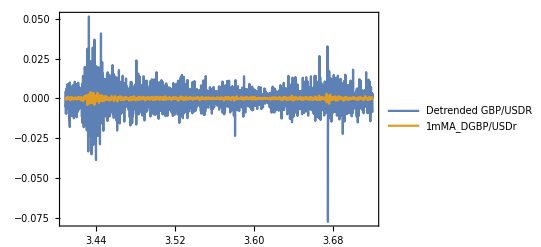

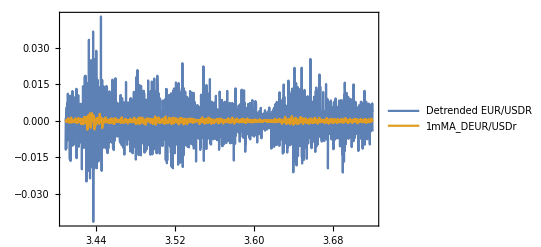

```mathematica
Dgbpusdr= Take[Drop[gbpusdr,10],2456]-mMAgbpusdr;
Deurusdr= Take[Drop[eurusdr,10],2456]-mMAeurusdr;
DGBPUSDr=Table[{date[[i+10]],Dgbpusdr[[i+10]]},{i,1,2435}];
DEURUSDr=Table[{date[[i+10]],Deurusdr[[i+10]]},{i,1,2435}];
mMADgbpusdr=MovingAverage[Dgbpusdr,21];
mMADeurusdr=MovingAverage[Deurusdr,21];
mMADGBPUSDr=Table[{date[[i+10]],mMADgbpusdr[[i]]},{i,1,2435}];mMADEURUSDr=Table[{date[[i+10]],mMADeurusdr[[i]]},{i,1,2435}];
DateListPlot[{DGBPUSDr,mMADGBPUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended GBP/USDR","1mMA_DGBP/USDr"},Above]]
DateListPlot[{DEURUSDr,mMADEURUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended EUR/USDR","1mMA_DEUR/USDr"},Above]]
```

I have tried 2, 3, 4-year size of observation, the variance gamma process can not fit detrended log returns in the most of the time. So I choose 1-year observation as the rolling window. In order to generate 10 one-step ahead forecasts, I need to make sure 10 continues rolling windows must be successful (variance gamma process must be fitted)

```mathematica
(*Drift estimation*)
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Subscript[gbpdiff, n,j]=Take[Drop[gbpdiff,252*(n-1)+j-1],273];
Subscript[eurdiff, n,j]=Take[Drop[eurdiff,252*(n-1)+j-1],273];
Subscript[mMAgbpusdr, n,j]=Take[Drop[mMAgbpusdr,252*(n-1)+j-1],273];
Subscript[mMAeurusdr, n,j]=Take[Drop[mMAeurusdr,252*(n-1)+j-1],273]]]
```

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
For[t=1,t≤252,t++,
Subscript[gbpdiff, n,j,t]=Take[Drop[Subscript[gbpdiff, n,j],t-1],21];
Subscript[eurdiff, n,j,t]=Take[Drop[Subscript[eurdiff, n,j],t-1],21];
Subscript[lm1, n,j,t]=LinearModelFit[Subscript[gbpdiff, n,j,t],x,x];
Subscript[lm2, n,j,t]=LinearModelFit[Subscript[eurdiff, n,j,t],x,x];
Subscript[b1, n,j,t]=Subscript[lm1, n,j,t]["BestFitParameters"][[2]];
Subscript[b2, n,j,t]=Subscript[lm2, n,j,t]["BestFitParameters"][[2]]];
Subscript[b1, n,j]=Table[Subscript[b1, n,j,t],{t,1,252}];
Subscript[b2, n,j]=Table[Subscript[b2, n,j,t],{t,1,252}];
Subscript[empb1, n,j]=EmpiricalDistribution[Subscript[b1, n,j]];
Subscript[empb2, n,j]=EmpiricalDistribution[Subscript[b2, n,j]];
Subscript[empMAr1, n,j]=EmpiricalDistribution[Subscript[mMAgbpusdr, n,j]];
Subscript[empMAr2, n,j]=EmpiricalDistribution[Subscript[mMAeurusdr, n,j]]]]
```

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Subscript[k1, n,j]=Minimize[{Abs[(Quantile[Subscript[empMAr1, n,j],0.975]-Quantile[Subscript[empMAr1, n,j],0.025])-x*(Quantile[Subscript[empb1, n,j],0.975]-Quantile[Subscript[empb1, n,j],0.025])],x>0},x];
Subscript[k2, n,j]=Minimize[{Abs[(Quantile[Subscript[empMAr2, n,j],0.975]-Quantile[Subscript[empMAr2, n,j],0.025])-x*(Quantile[Subscript[empb2, n,j],0.975]-Quantile[Subscript[empb2, n,j],0.025])],x>0},x]];
Print ["Period=",n];
Print[Subscript[k1, n,9][[2]]];
Print[Subscript[k2, n,9][[2]]];
Print[]]
```

Period=1

{x→10.4705}

{x→11.6766}

Period=2

{x→20.9791}

{x→16.914}

Period=3

{x→15.3256}

{x→15.9654}

Period=4

{x→16.6358}

{x→8.92945}

Period=5

{x→15.9853}

{x→19.5425}

Period=6

{x→25.9344}

{x→19.5434}

Period=7

{x→9.69073}

{x→10.2176}

Period=8

{x→23.3164}

{x→16.17}

```mathematica
K1={10.470539820992292,20.979117612571212,15.325632081090331,16.63578726979469,15.985327110208422,25.9344295801042939,9.690733292622012,23.31637045812859};
K2={11.676595405834066,16.9139521288565,15.965406520746045,8.929451581114918,19.54245254531515,19.543388858285258,10.217577433089062,16.16996801462872};
```

```mathematica
For[n=1,n<9,n++,
Subscript[K1, n]=K1[[n]];
Subscript[K2, n]=K2[[n]];
For[j=1,j<11,j++,
For[t=1,t≤252,t++,
Subscript[msf1, n,j,t]=Subscript[K1, n]*Subscript[b1, n,j,t];
Subscript[msf2, n,j,t]=Subscript[K2, n]*Subscript[b2, n,j,t]];
Subscript[msf1, n,j]=Table[Subscript[msf1, n,j,t],{t,1,252}];
Subscript[msf2, n,j]=Table[Subscript[msf2, n,j,t],{t,1,252}]]]
```

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Subscript[gbpusdr, n,j]=Take[Drop[Drop[gbpusdr,20],252*(n-1)+j-1],252];
Subscript[eurusdr, n,j]=Take[Drop[Drop[eurusdr,20],252*(n-1)+j-1],252];
Subscript[L1, n,j]=(Subscript[gbpusdr, n,j]+Subscript[msf1, n,j])*100;
Subscript[L2, n,j]=(Subscript[eurusdr, n,j]+Subscript[msf2, n,j])*100]]
```

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Print["Period=",n,",",j];
Print[NSolve[m1+θ1==Mean[Subscript[L1, n,j]]&&σ1^2+θ1^2==Variance[Subscript[L1, n,j]]&&(2*θ1^3+3σ1^2*θ1)/(σ1^2+θ1^2)^1.5==Skewness[Subscript[L1, n,j]]&&σ1>0,{m1,θ1,σ1},Reals]];
Print[NSolve[m2+θ2==Mean[Subscript[L2, n,j]]&&σ2^2+θ2^2==Variance[Subscript[L2, n,j]]&&(2*θ2^3+3σ2^2*θ2)/(σ2^2+θ2^2)^1.5==Skewness[Subscript[L2, n,j]]&&σ2>0,{m2,θ2,σ2},Reals]]]]
```

Period=1,1

{{θ1→-0.11742,σ1→1.08619,m1→-0.0636066}}

{{θ2→0.0341594,σ2→1.02341,m2→-0.108671}}

Period=1,2

{{θ1→-0.121137,σ1→1.08621,m1→-0.0557782}}

{{θ2→0.03559,σ2→1.02324,m2→-0.111545}}

Period=1,3

{{θ1→-0.121037,σ1→1.08704,m1→-0.0550275}}

{{θ2→0.0337832,σ2→1.02741,m2→-0.104311}}

Period=1,4

{{θ1→-0.118133,σ1→1.09172,m1→-0.0639315}}

{{θ2→0.0329799,σ2→1.02576,m2→-0.101277}}

Period=1,5

{{θ1→-0.119958,σ1→1.10154,m1→-0.0726509}}

{{θ2→0.0361135,σ2→1.02873,m2→-0.110399}}

Period=1,6

{{θ1→-0.118879,σ1→1.10237,m1→-0.0750303}}

{{θ2→0.0359057,σ2→1.02991,m2→-0.111303}}

Period=1,7

{{θ1→-0.118831,σ1→1.10451,m1→-0.0727053}}

{{θ2→0.033409,σ2→1.03137,m2→-0.105661}}

Period=1,8

{{θ1→-0.113618,σ1→1.1079,m1→-0.0852545}}

{{θ2→0.0362338,σ2→1.03359,m2→-0.113101}}

Period=1,9

{{θ1→-0.111542,σ1→1.10622,m1→-0.0909351}}

{{θ2→0.0365062,σ2→1.0401,m2→-0.123965}}

Period=1,10

{{θ1→-0.108232,σ1→1.1064,m1→-0.0977347}}

{{θ2→0.0379722,σ2→1.04064,m2→-0.12716}}

Period=2,1

{{θ1→0.07495,σ1→0.870388,m1→-0.0441171}}

{{θ2→0.224452,σ2→0.707285,m2→-0.213623}}

Period=2,2

{{θ1→0.0760031,σ1→0.870271,m1→-0.0462176}}

{{θ2→0.224667,σ2→0.708249,m2→-0.215313}}

Period=2,3

{{θ1→0.0789625,σ1→0.868919,m1→-0.0525269}}

{{θ2→0.227642,σ2→0.7029,m2→-0.223131}}

Period=2,4

{{θ1→0.0873256,σ1→0.859092,m1→-0.0536659}}

{{θ2→0.223681,σ2→0.703787,m2→-0.213967}}

Period=2,5

{{θ1→0.122031,σ1→0.836282,m1→-0.0776393}}

{{θ2→0.231845,σ2→0.695148,m2→-0.217776}}

Period=2,6

{{θ1→0.123106,σ1→0.834848,m1→-0.0777481}}

{{θ2→0.239171,σ2→0.686879,m2→-0.220611}}

Period=2,7

{{θ1→0.118874,σ1→0.84196,m1→-0.084282}}

{{θ2→0.241717,σ2→0.687734,m2→-0.229566}}

Period=2,8

{{θ1→0.124218,σ1→0.833643,m1→-0.0822052}}

{{θ2→0.243933,σ2→0.682372,m2→-0.2249}}

Period=2,9

{{θ1→0.124925,σ1→0.834279,m1→-0.0842401}}

{{θ2→0.278209,σ2→0.654836,m2→-0.251766}}

Period=2,10

{{θ1→0.124335,σ1→0.833201,m1→-0.0819272}}

{{θ2→0.277489,σ2→0.653103,m2→-0.247514}}

Period=3,1

{{θ1→0.000586935,σ1→0.680304,m1→0.0351139}}

{{θ2→0.0144376,σ2→0.778724,m2→0.0247911}}

Period=3,2

{{θ1→-0.0010573,σ1→0.680787,m1→0.0385975}}

{{θ2→0.0110014,σ2→0.777878,m2→0.0326065}}

Period=3,3

{{θ1→-0.00102339,σ1→0.680791,m1→0.0385294}}

{{θ2→0.00967346,σ2→0.778199,m2→0.0353414}}

Period=3,4

{{θ1→-0.00289839,σ1→0.681414,m1→0.0425778}}

{{θ2→0.00991429,σ2→0.777917,m2→0.0346816}}

Period=3,5

{{θ1→-0.00109978,σ1→0.682663,m1→0.0381987}}

{{θ2→0.00770646,σ2→0.777523,m2→0.0392973}}

Period=3,6

{{θ1→-0.00230086,σ1→0.680509,m1→0.0424269}}

{{θ2→0.00763862,σ2→0.777488,m2→0.0394491}}

Period=3,7

{{θ1→0.00753195,σ1→0.676077,m1→0.0446517}}

{{θ2→0.00430198,σ2→0.775422,m2→0.0487383}}

Period=3,8

{{θ1→0.00695157,σ1→0.676335,m1→0.0459035}}

{{θ2→0.00502934,σ2→0.775114,m2→0.0471743}}

Period=3,9

{{θ1→0.00462354,σ1→0.675521,m1→0.0510811}}

{{θ2→0.00208742,σ2→0.775338,m2→0.0533677}}

Period=3,10

{{θ1→0.0044516,σ1→0.675447,m1→0.0514538}}

{{θ2→0.000439445,σ2→0.77615,m2→0.0570527}}

Period=4,1

{{θ1→-0.00470922,σ1→0.589974,m1→-0.0344588}}

{{θ2→-0.0602552,σ2→0.749975,m2→0.0237659}}

Period=4,2

{{θ1→-0.0032598,σ1→0.589158,m1→-0.037828}}

{{θ2→-0.0595865,σ2→0.74957,m2→0.0221367}}

Period=4,3

{{θ1→-0.00404775,σ1→0.591813,m1→-0.0335541}}

{{θ2→-0.0567542,σ2→0.749613,m2→0.0161673}}

Period=4,4

{{θ1→-0.0020018,σ1→0.590819,m1→-0.0383288}}

{{θ2→-0.0538102,σ2→0.749305,m2→0.0097517}}

Period=4,5

{{θ1→-0.00200531,σ1→0.591113,m1→-0.0386163}}

{{θ2→-0.0507579,σ2→0.75173,m2→0.00194389}}

Period=4,6

{{θ1→-0.00245846,σ1→0.59115,m1→-0.0377059}}

{{θ2→-0.0525355,σ2→0.751567,m2→0.00553859}}

Period=4,7

{{θ1→-0.00600675,σ1→0.587179,m1→-0.0429967}}

{{θ2→-0.0486628,σ2→0.753154,m2→-0.00408584}}

Period=4,8

{{θ1→-0.00389851,σ1→0.586611,m1→-0.0475938}}

{{θ2→-0.0479799,σ2→0.753059,m2→-0.0054949}}

Period=4,9

{{θ1→-0.00432163,σ1→0.588004,m1→-0.0454977}}

{{θ2→-0.0470803,σ2→0.755828,m2→-0.00388998}}

Period=4,10

{{θ1→-0.00334328,σ1→0.589816,m1→-0.0489686}}

{{θ2→-0.0439099,σ2→0.758679,m2→-0.0140366}}

Period=5,1

{{θ1→-0.0445207,σ1→0.452009,m1→0.0077324}}

{{θ2→0.0424037,σ2→0.583141,m2→-0.073283}}

Period=5,2

{{θ1→-0.04414,σ1→0.452079,m1→0.0069775}}

{{θ2→0.0416074,σ2→0.583789,m2→-0.071434}}

Period=5,3

{{θ1→-0.0461781,σ1→0.451871,m1→0.00195165}}

{{θ2→0.0405935,σ2→0.586194,m2→-0.0724872}}

Period=5,4

{{θ1→-0.0457999,σ1→0.452062,m1→0.00117175}}

{{θ2→0.0389048,σ2→0.585876,m2→-0.0688538}}

Period=5,5

{{θ1→-0.046596,σ1→0.450303,m1→0.00399698}}

{{θ2→0.0396577,σ2→0.58236,m2→-0.0658912}}

Period=5,6

{{θ1→-0.0469147,σ1→0.450412,m1→0.00471119}}

{{θ2→0.0414917,σ2→0.583685,m2→-0.0709059}}

Period=5,7

{{θ1→-0.046072,σ1→0.450165,m1→0.0104809}}

{{θ2→0.0413174,σ2→0.58044,m2→-0.0664045}}

Period=5,8

{{θ1→-0.0477784,σ1→0.45095,m1→0.0149442}}

{{θ2→0.0394463,σ2→0.581704,m2→-0.0620806}}

Period=5,9

{{θ1→-0.0468119,σ1→0.449143,m1→0.0105095}}

{{θ2→0.0399447,σ2→0.580889,m2→-0.0703278}}

Period=5,10

{{θ1→-0.0477278,σ1→0.446524,m1→0.0146187}}

{{θ2→0.0450506,σ2→0.576348,m2→-0.0728858}}

Period=6,1

{{θ1→-0.0916309,σ1→0.442883,m1→0.162161}}

{{θ2→-0.0321754,σ2→0.448772,m2→0.0549322}}

Period=6,2

{{θ1→-0.0936018,σ1→0.44264,m1→0.166399}}

{{θ2→-0.0317786,σ2→0.448221,m2→0.0536618}}

Period=6,3

{{θ1→-0.0903283,σ1→0.439131,m1→0.165568}}

{{θ2→-0.0300317,σ2→0.444116,m2→0.0557141}}

Period=6,4

{{θ1→-0.0916399,σ1→0.438158,m1→0.168266}}

{{θ2→-0.0299609,σ2→0.444113,m2→0.0555711}}

Period=6,5

{{θ1→-0.091131,σ1→0.439391,m1→0.166616}}

{{θ2→-0.030073,σ2→0.444076,m2→0.055798}}

Period=6,6

{{θ1→-0.0915795,σ1→0.439418,m1→0.167572}}

{{θ2→-0.0306012,σ2→0.441707,m2→0.0590584}}

Period=6,7

{{θ1→-0.0914513,σ1→0.441355,m1→0.161235}}

{{θ2→-0.0314822,σ2→0.44546,m2→0.0560571}}

Period=6,8

{{θ1→-0.0893697,σ1→0.44156,m1→0.156637}}

{{θ2→-0.0303201,σ2→0.444299,m2→0.0525776}}

Period=6,9

{{θ1→-0.0898947,σ1→0.441122,m1→0.157727}}

{{θ2→-0.0283784,σ2→0.440212,m2→0.0542919}}

Period=6,10

{{θ1→-0.0901711,σ1→0.441038,m1→0.15826}}

{{θ2→-0.0287056,σ2→0.438183,m2→0.0568018}}

Period=7,1

{{θ1→-0.0646864,σ1→0.387148,m1→-0.00111641}}

{{θ2→-0.0816013,σ2→0.454702,m2→-0.0549281}}

Period=7,2

{{θ1→-0.0649288,σ1→0.386302,m1→-0.00168943}}

{{θ2→-0.0801312,σ2→0.454565,m2→-0.058185}}

Period=7,3

{{θ1→-0.050063,σ1→0.396602,m1→-0.0103922}}

{{θ2→-0.0551023,σ2→0.469853,m2→-0.0771781}}

Period=7,4

{{θ1→-0.0498671,σ1→0.396566,m1→-0.0108115}}

{{θ2→-0.0449186,σ2→0.477992,m2→-0.0828747}}

Period=7,5

{{θ1→-0.0498665,σ1→0.397057,m1→-0.0112423}}

{{θ2→-0.0441519,σ2→0.478159,m2→-0.0844046}}

Period=7,6

{{θ1→-0.0497886,σ1→0.396759,m1→-0.0117122}}

{{θ2→-0.0436916,σ2→0.480635,m2→-0.0822375}}

Period=7,7

{{θ1→-0.0490902,σ1→0.395795,m1→-0.0117372}}

{{θ2→-0.0431125,σ2→0.47955,m2→-0.0820063}}

Period=7,8

{{θ1→-0.0500606,σ1→0.395809,m1→-0.00972497}}

{{θ2→-0.041886,σ2→0.479802,m2→-0.0844831}}

Period=7,9

{{θ1→-0.0488667,σ1→0.39743,m1→-0.0130505}}

{{θ2→-0.0399616,σ2→0.480924,m2→-0.0888595}}

Period=7,10

{{θ1→-0.0490936,σ1→0.39758,m1→-0.0124686}}

{{θ2→-0.0387638,σ2→0.48333,m2→-0.0932631}}

Period=8,1

{{θ1→0.0943187,σ1→0.603465,m1→-0.13857}}

{{θ2→0.0766368,σ2→0.753671,m2→-0.0863807}}

Period=8,2

{{θ1→0.0942892,σ1→0.603477,m1→-0.138512}}

{{θ2→0.0764033,σ2→0.753601,m2→-0.0858662}}

Period=8,3

{{θ1→0.0926629,σ1→0.601533,m1→-0.138212}}

{{θ2→0.0752377,σ2→0.747953,m2→-0.0899801}}

Period=8,4

{{θ1→0.0932555,σ1→0.606883,m1→-0.133451}}

{{θ2→0.0770685,σ2→0.749714,m2→-0.0906827}}

Period=8,5

{{θ1→0.0933538,σ1→0.606004,m1→-0.132606}}

{{θ2→0.074451,σ2→0.750075,m2→-0.085297}}

Period=8,6

{{θ1→0.0900027,σ1→0.61172,m1→-0.134605}}

{{θ2→0.0779887,σ2→0.749213,m2→-0.0929334}}

Period=8,7

{{θ1→0.0869228,σ1→0.612854,m1→-0.125324}}

{{θ2→0.0748525,σ2→0.748472,m2→-0.0854681}}

Period=8,8

{{θ1→0.0864798,σ1→0.616204,m1→-0.128877}}

{{θ2→0.0734847,σ2→0.748238,m2→-0.0825548}}

Period=8,9

{{θ1→0.0860208,σ1→0.6147,m1→-0.12628}}

{{θ2→0.0715038,σ2→0.747293,m2→-0.0777316}}

Period=8,10

{{θ1→0.0854906,σ1→0.614897,m1→-0.125234}}

{{θ2→0.0695145,σ2→0.745316,m2→-0.0715766}}

We generate 80 rolling windows, and obtain 3*80 parameters.

```mathematica
Subscript[θ1, 1,1]=-0.11741951698810713;Subscript[σ1, 1,1]=1.0861935995368575;Subscript[m1, 1,1]=-0.06360660444012395;
Subscript[θ2, 1,1]=0.034159364320383134;Subscript[σ2, 1,1]=1.0234097642719355;Subscript[m2, 1,1]=-0.10867148079573972;
Subscript[θ1, 1,2]=-0.12113651916034025;Subscript[σ1, 1,2]=1.0862139560376076;Subscript[m1, 1,2]=-0.05577818847868339;
Subscript[θ2, 1,2]=0.03559003243578753;Subscript[σ2, 1,2]=1.0232430991546932;Subscript[m2, 1,2]=-0.11154511858862845;
Subscript[θ1, 1,3]=-0.12103739687212826;Subscript[σ1, 1,3]=1.0870384315073895;Subscript[m1, 1,3]=-0.05502754351258214;
Subscript[θ2, 1,3]=0.03378319393562257;Subscript[σ2, 1,3]=1.027414121266888;Subscript[m2, 1,3]=-0.10431094571230944;
Subscript[θ1, 1,4]=-0.11813326679917853;Subscript[σ1, 1,4]=1.0917224703501274;Subscript[m1, 1,4]=-0.06393154955843718;
Subscript[θ2, 1,4]=0.03297989476014157;Subscript[σ2, 1,4]=1.0257566467404295;Subscript[m2, 1,4]=-0.10127727521844522;
Subscript[θ1, 1,5]=-0.1199580724995246;Subscript[σ1, 1,5]=1.101543063786636;Subscript[m1, 1,5]=-0.0726509272042518;
Subscript[θ2, 1,5]=0.03611350386671662;Subscript[σ2, 1,5]=1.0287330428263284;Subscript[m2, 1,5]=-0.11039926027154619;
Subscript[θ1, 1,6]=-0.11887867586275618;Subscript[σ1, 1,6]=1.1023650694291722;Subscript[m1, 1,6]=-0.07503027523299592;
Subscript[θ2, 1,6]=0.03590573957654228;Subscript[σ2, 1,6]=1.0299129606828634;Subscript[m2, 1,6]=-0.11130338422103175;
Subscript[θ1, 1,7]=-0.11883145174698904;Subscript[σ1, 1,7]=1.1045129186807672;Subscript[m1, 1,7]=-0.07270534404184885;
Subscript[θ2, 1,7]=0.03340901409737155;Subscript[σ2, 1,7]=1.0313668091063182;Subscript[m2, 1,7]=-0.10566052770767434;
Subscript[θ1, 1,8]=-0.11361752215217287;Subscript[σ1, 1,8]=1.1078997105710735;Subscript[m1, 1,8]=-0.08525448513041008;
Subscript[θ2, 1,8]=0.03623376321539718;Subscript[σ2, 1,8]=1.0335858137913194;Subscript[m2, 1,8]=-0.11310079960287409;
Subscript[θ1, 1,9]=-0.11154219763624058;Subscript[σ1, 1,9]=1.106222620752177;Subscript[m1, 1,9]=-0.09093505271001177;
Subscript[θ2, 1,9]=0.036506196605235124;Subscript[σ2, 1,9]=1.040101222305938;Subscript[m2, 1,9]=-0.12396507533550735;
Subscript[θ1, 1,10]=-0.1082324771849363;Subscript[σ1, 1,10]=1.1063995136772184;Subscript[m1, 1,10]=-0.09773468801556627;
Subscript[θ2, 1,10]=0.03797217132057455;Subscript[σ2, 1,10]=1.0406393377983438;Subscript[m2, 1,10]=-0.12716037262424398;
Subscript[θ1, 2,1]=0.07494999282506705;Subscript[σ1, 2,1]=0.8703880917296211;Subscript[m1, 2,1]=-0.04411714034597736;
Subscript[θ2, 2,1]=0.22445156277590003;Subscript[σ2, 2,1]=0.7072845956829398;Subscript[m2, 2,1]=-0.21362296684382664;
Subscript[θ1, 2,2]=0.07600306601316019;Subscript[σ1, 2,2]=0.8702713480358526;Subscript[m1, 2,2]=-0.04621759153873476;
Subscript[θ2, 2,2]=0.22466688169341448;Subscript[σ2, 2,2]=0.7082486228822203;Subscript[m2, 2,2]=-0.21531255387433612;
Subscript[θ1, 2,3]=0.07896247891687944;Subscript[σ1, 2,3]=0.8689187719285334;Subscript[m1, 2,3]=-0.05252694430815065;
Subscript[θ2, 2,3]=0.22764159762390576;Subscript[σ2, 2,3]=0.7029004794782985;Subscript[m2, 2,3]=-0.22313103393818623;
Subscript[θ1, 2,4]=0.087325626329408;Subscript[σ1, 2,4]=0.859092080729922;Subscript[m1, 2,4]=-0.053665852073382946;
Subscript[θ2, 2,4]=0.2236814438825398;Subscript[σ2, 2,4]=0.7037873853588165;Subscript[m2, 2,4]=-0.21396656910882833;
Subscript[θ1, 2,5]=0.12203089527991015;Subscript[σ1, 2,5]=0.8362817636567905;Subscript[m1, 2,5]=-0.07763931127786211;
Subscript[θ2, 2,5]=0.23184533878615446;Subscript[σ2, 2,5]=0.6951484778419617;Subscript[m2, 2,5]=-0.21777586987205558;
Subscript[θ1, 2,6]=0.12310559736746245;Subscript[σ1, 2,6]=0.8348481724164052;Subscript[m1, 2,6]=-0.07774810770446464;
Subscript[θ2, 2,6]=0.2391713677787323;Subscript[σ2, 2,6]=0.6868792132707492;Subscript[m2, 2,6]=-0.22061091487554163;
Subscript[θ1, 2,7]=0.11887376451039142;Subscript[σ1, 2,7]=0.8419598038595876;Subscript[m1, 2,7]=-0.08428198358221209;
Subscript[θ2, 2,7]=0.24171706067577503;Subscript[σ2, 2,7]=0.6877336732701154;Subscript[m2, 2,7]=-0.2295664813750625;
Subscript[θ1, 2,8]=0.12421806544587945;Subscript[σ1, 2,8]=0.8336427519214324;Subscript[m1, 2,8]=-0.08220521498257197;
Subscript[θ2, 2,8]=0.24393280709030116;Subscript[σ2, 2,8]=0.6823723262688004;Subscript[m2, 2,8]=-0.22490014995185587;
Subscript[θ1, 2,9]=0.12492532100262362;Subscript[σ1, 2,9]=0.8342785347186774;Subscript[m1, 2,9]=-0.08424006086231589;
Subscript[θ2, 2,9]=0.2782094446316088;Subscript[σ2, 2,9]=0.6548361327399312;Subscript[m2, 2,9]=-0.2517663116475385;
Subscript[θ1, 2,10]=0.12433525753648307;Subscript[σ1, 2,10]=0.8332010944578387;Subscript[m1, 2,10]=-0.08192718405715331;
Subscript[θ2, 2,10]=0.277488600517241;Subscript[σ2, 2,10]=0.6531030371665264;Subscript[m2, 2,10]=-0.24751392156833943;
Subscript[θ1, 3,1]=0.0005869351126895992;Subscript[σ1, 3,1]=0.6803040686053732;Subscript[m1, 3,1]=0.035113853154226576;
Subscript[θ2, 3,1]=0.014437566226210929;Subscript[σ2, 3,1]=0.7787235249864053;Subscript[m2, 3,1]=0.024791075364100704;
Subscript[θ1, 3,2]=-0.0010572976835885495;Subscript[σ1, 3,2]=0.6807873424953825;Subscript[m1, 3,2]=0.0385975476185038;
Subscript[θ2, 3,2]=0.011001431808225694;Subscript[σ2, 3,2]=0.7778776090344137;Subscript[m2, 3,2]=0.03260646983024397;
Subscript[θ1, 3,3]=-0.0010233865664223839;Subscript[σ1, 3,3]=0.6807911020779899;Subscript[m1, 3,3]=0.038529403670091784;
Subscript[θ2, 3,3]=0.009673458351987865;Subscript[σ2, 3,3]=0.778199499136873;Subscript[m2, 3,3]=0.0353414366926008;
Subscript[θ1, 3,4]=-0.002898394586564186;Subscript[σ1, 3,4]=0.6814140903163658;Subscript[m1, 3,4]=0.04257783038960307;
Subscript[θ2, 3,4]=0.009914287158376901;Subscript[σ2, 3,4]=0.7779174307389226;Subscript[m2, 3,4]=0.03468160184853154;
Subscript[θ1, 3,5]=-0.001099776001255754;Subscript[σ1, 3,5]=0.6826625492869557;Subscript[m1, 3,5]=0.03819865931960021;
Subscript[θ2, 3,5]=0.007706463552401607;Subscript[σ2, 3,5]=0.7775232745182825;Subscript[m2, 3,5]=0.03929734632433907;
Subscript[θ1, 3,6]=-0.0023008582083545045;Subscript[σ1, 3,6]=0.680508844421611;Subscript[m1, 3,6]=0.04242690725982421;
Subscript[θ2, 3,6]=0.0076386195761601605;Subscript[σ2, 3,6]=0.777487809511013;Subscript[m2, 3,6]=0.03944910620536625;
Subscript[θ1, 3,7]=0.007531950272963182;Subscript[σ1, 3,7]=0.6760769379525612;Subscript[m1, 3,7]=0.044651686790363077;
Subscript[θ2, 3,7]=0.004301983829295004;Subscript[σ2, 3,7]=0.7754217812575929;Subscript[m2, 3,7]=0.04873832223547935;
Subscript[θ1, 3,8]=0.00695156882548435;Subscript[σ1, 3,8]=0.6763351141144986;Subscript[m1, 3,8]=0.04590352338172856;
Subscript[θ2, 3,8]=0.005029340259541391;Subscript[σ2, 3,8]=0.7751144324972815;Subscript[m2, 3,8]=0.0471742736158596;
Subscript[θ1, 3,9]=0.004623537190943886;Subscript[σ1, 3,9]=0.6755212529385506;Subscript[m1, 3,9]=0.051081069487774716;
Subscript[θ2, 3,9]=0.0020874190050535774;Subscript[σ2, 3,9]=0.7753377280658591;Subscript[m2, 3,9]=0.05336765058245746;
Subscript[θ1, 3,10]=0.004451600480026624;Subscript[σ1, 3,10]=0.6754472068014563;Subscript[m1, 3,10]=0.05145375383748928;
Subscript[θ2, 3,10]=0.0004394450899322141;Subscript[σ2, 3,10]=0.7761498819994297;Subscript[m2, 3,10]=0.057052700735780525;
Subscript[θ1, 4,1]=-0.004709223531076055;Subscript[σ1, 4,1]=0.5899740914144015;Subscript[m1, 4,1]=-0.0344587954701659;
Subscript[θ2, 4,1]=-0.0602552306699949;Subscript[σ2, 4,1]=0.7499747490868925;Subscript[m2, 4,1]=0.02376591526469673;
Subscript[θ1, 4,2]=-0.0032598000755567538;Subscript[σ1, 4,2]=0.589157804148629;Subscript[m1, 4,2]=-0.03782802215835797;
Subscript[θ2, 4,2]=-0.05958654523040024;Subscript[σ2, 4,2]=0.7495699046077319;Subscript[m2, 4,2]=0.022136731848922682;
Subscript[θ1, 4,3]=-0.004047753156487758;Subscript[σ1, 4,3]=0.5918127623974021;Subscript[m1, 4,3]=-0.033554055102376204;
Subscript[θ2, 4,3]=-0.05675420150081251;Subscript[σ2, 4,3]=0.7496128227008553;Subscript[m2, 4,3]=0.016167313638149744;
Subscript[θ1, 4,4]=-0.0020018020738175758;Subscript[σ1, 4,4]=0.590819158647962;Subscript[m1, 4,4]=-0.03832881098708796;
Subscript[θ2, 4,4]=-0.05381016379387821;Subscript[σ2, 4,4]=0.7493046513368486;Subscript[m2, 4,4]=0.009751701547775653;
Subscript[θ1, 4,5]=-0.0020053093290442834;Subscript[σ1, 4,5]=0.5911132799167879;Subscript[m1, 4,5]=-0.038616304267473006;
Subscript[θ2, 4,5]=-0.05075790682101261;Subscript[σ2, 4,5]=0.7517302956915852;Subscript[m2, 4,5]=0.0019438935948365987;
Subscript[θ1, 4,6]=-0.0024584593921130864;Subscript[σ1, 4,6]=0.5911501249869832;Subscript[m1, 4,6]=-0.03770592842122034;
Subscript[θ2, 4,6]=-0.05253545707520286;Subscript[σ2, 4,6]=0.7515669333419577;Subscript[m2, 4,6]=0.005538587036455538;
Subscript[θ1, 4,7]=-0.006006752756608913;Subscript[σ1, 4,7]=0.5871792245825048;Subscript[m1, 4,7]=-0.042996739424524436;
Subscript[θ2, 4,7]=-0.04866277015816301;Subscript[σ2, 4,7]=0.7531542706575466;Subscript[m2, 4,7]=-0.004085835473783481;
Subscript[θ1, 4,8]=-0.0038985109346571906;Subscript[σ1, 4,8]=0.5866113166833836;Subscript[m1, 4,8]=-0.047593799786351275;
Subscript[θ2, 4,8]=-0.04797993835673446;Subscript[σ2, 4,8]=0.753059364727554;Subscript[m2, 4,8]=-0.005494898359454277;
Subscript[θ1, 4,9]=-0.004321625568981247;Subscript[σ1, 4,9]=0.5880037528882949;Subscript[m1, 4,9]=-0.045497654635377534;
Subscript[θ2, 4,9]=-0.047080268933139297;Subscript[σ2, 4,9]=0.755827956642518;Subscript[m2, 4,9]=-0.003889979516575895;
Subscript[θ1, 4,10]=-0.0033432780393759355;Subscript[σ1, 4,10]=0.5898155729104403;Subscript[m1, 4,10]=-0.048968630210044765;
Subscript[θ2, 4,10]=-0.04390990872554116;Subscript[σ2, 4,10]=0.758679094257014;Subscript[m2, 4,10]=-0.014036600963159451;
Subscript[θ1, 5,1]=-0.044520715772021525;Subscript[σ1, 5,1]=0.4520094786849512;Subscript[m1, 5,1]=0.007732401759668009;
Subscript[θ2, 5,1]=0.042403684749313435;Subscript[σ2, 5,1]=0.5831410332751161;Subscript[m2, 5,1]=-0.07328302367742465;
Subscript[θ1, 5,2]=-0.04413999414455298;Subscript[σ1, 5,2]=0.45207921374508225;Subscript[m1, 5,2]=0.006977498745073474;
Subscript[θ2, 5,2]=0.04160741474207501;Subscript[σ2, 5,2]=0.583789086377808;Subscript[m2, 5,2]=-0.07143403459650269;
Subscript[θ1, 5,3]=-0.046178120502873;Subscript[σ1, 5,3]=0.4518707652451322;Subscript[m1, 5,3]=0.0019516519809542054;
Subscript[θ2, 5,3]=0.040593456857070505;Subscript[σ2, 5,3]=0.5861942683126711;Subscript[m2, 5,3]=-0.07248715091977931;
Subscript[θ1, 5,4]=-0.04579986826141778;Subscript[σ1, 5,4]=0.45206161066701495;Subscript[m1, 5,4]=0.0011717518648992759;
Subscript[θ2, 5,4]=0.038904847722932075;Subscript[σ2, 5,4]=0.5858757967219819;Subscript[m2, 5,4]=-0.06885380142658859;
Subscript[θ1, 5,5]=-0.046595991826548944;Subscript[σ1, 5,5]=0.4503030643044161;Subscript[m1, 5,5]=0.003996977888002379;
Subscript[θ2, 5,5]=0.039657705539684444;Subscript[σ2, 5,5]=0.582359518246354;Subscript[m2, 5,5]=-0.06589117977790278;
Subscript[θ1, 5,6]=-0.046914728325182474;Subscript[σ1, 5,6]=0.4504117651348179;Subscript[m1, 5,6]=0.004711193165478453;
Subscript[θ2, 5,6]=0.041491678130683655;Subscript[σ2, 5,6]=0.5836847974753366;Subscript[m2, 5,6]=-0.07090592197412962;
Subscript[θ1, 5,7]=-0.046071971839791545;Subscript[σ1, 5,7]=0.450165048791044;Subscript[m1, 5,7]=0.010480863027910035;
Subscript[θ2, 5,7]=0.041317410921518714;Subscript[σ2, 5,7]=0.580439999620925;Subscript[m2, 5,7]=-0.06640452759489371;
Subscript[θ1, 5,8]=-0.04777841890168343;Subscript[σ1, 5,8]=0.45095042366319094;Subscript[m1, 5,8]=0.014944176590514065;
Subscript[θ2, 5,8]=0.039446291424064646;Subscript[σ2, 5,8]=0.5817042070532256;Subscript[m2, 5,8]=-0.06208062014795586;
Subscript[θ1, 5,9]=-0.04681185375427555;Subscript[σ1, 5,9]=0.4491426033621523;Subscript[m1, 5,9]=0.010509452284907878;
Subscript[θ2, 5,9]=0.03994467228728829;Subscript[σ2, 5,9]=0.5808887128556659;Subscript[m2, 5,9]=-0.07032780314731102;
Subscript[θ1, 5,10]=-0.04772781358974484;Subscript[σ1, 5,10]=0.44652428229918745;Subscript[m1, 5,10]=0.01461865352410692;
Subscript[θ2, 5,10]=0.04505059571433192;Subscript[σ2, 5,10]=0.5763477787440908;Subscript[m2, 5,10]=-0.07288583383593777;
Subscript[θ1, 6,1]=-0.09163092286359226;Subscript[σ1, 6,1]=0.4428827208930777;Subscript[m1, 6,1]=0.16216107864636242;
Subscript[θ2, 6,1]=-0.032175403565386236;Subscript[σ2, 6,1]=0.44877172997566483;Subscript[m2, 6,1]=0.054932227132322126;
Subscript[θ1, 6,2]=-0.09360181180227539;Subscript[σ1, 6,2]=0.4426398872625877;Subscript[m1, 6,2]=0.16639879456632606;
Subscript[θ2, 6,2]=-0.03177856761300573;Subscript[σ2, 6,2]=0.4482211647630106;Subscript[m2, 6,2]=0.05366176703919124;
Subscript[θ1, 6,3]=-0.09032834256069254;Subscript[σ1, 6,3]=0.43913143155227613;Subscript[m1, 6,3]=0.16556808915353438;
Subscript[θ2, 6,3]=-0.030031697583248678;Subscript[σ2, 6,3]=0.44411635546556333;Subscript[m2, 6,3]=0.05571412581376971;
Subscript[θ1, 6,4]=-0.09163988221543856;Subscript[σ1, 6,4]=0.4381577588000179;Subscript[m1, 6,4]=0.16826572588809302;
Subscript[θ2, 6,4]=-0.02996092257402717;Subscript[σ2, 6,4]=0.44411306373393933;Subscript[m2, 6,4]=0.05557105015681979;
Subscript[θ1, 6,5]=-0.09113103895988262;Subscript[σ1, 6,5]=0.4393914062424629;Subscript[m1, 6,5]=0.16661608990000465;
Subscript[θ2, 6,5]=-0.030072960156438896;Subscript[σ2, 6,5]=0.44407592125838985;Subscript[m2, 6,5]=0.055798007599759225;
Subscript[θ1, 6,6]=-0.09157946842938243;Subscript[σ1, 6,6]=0.4394180496566812;Subscript[m1, 6,6]=0.16757169306044312;
Subscript[θ2, 6,6]=-0.030601153908285647;Subscript[σ2, 6,6]=0.4417066321770012;Subscript[m2, 6,6]=0.059058367966807884;
Subscript[θ1, 6,7]=-0.09145133142485903;Subscript[σ1, 6,7]=0.44135463045547896;Subscript[m1, 6,7]=0.1612351322574423;
Subscript[θ2, 6,7]=-0.03148223852323092;Subscript[σ2, 6,7]=0.4454597997477604;Subscript[m2, 6,7]=0.05605708140997756;
Subscript[θ1, 6,8]=-0.0893696905761813;Subscript[σ1, 6,8]=0.4415595492543312;Subscript[m1, 6,8]=0.15663732633591465;
Subscript[θ2, 6,8]=-0.03032012035309689;Subscript[σ2, 6,8]=0.4442989676031089;Subscript[m2, 6,8]=0.05257759925624359;
Subscript[θ1, 6,9]=-0.08989473346139662;Subscript[σ1, 6,9]=0.4411221418008316;Subscript[m1, 6,9]=0.15772693448570824;
Subscript[θ2, 6,9]=-0.028378392012232523;Subscript[σ2, 6,9]=0.44021241328352323;Subscript[m2, 6,9]=0.0542919253977739;
Subscript[θ1, 6,10]=-0.09017108638667168;Subscript[σ1, 6,10]=0.4410375219562981;Subscript[m1, 6,10]=0.1582604308020522;
Subscript[θ2, 6,10]=-0.028705611459534024;Subscript[σ2, 6,10]=0.4381834704744774;Subscript[m2, 6,10]=0.05680184190881621;
Subscript[θ1, 7,1]=-0.06468641174266689;Subscript[σ1, 7,1]=0.3871475583277125;Subscript[m1, 7,1]=-0.0011164123231802853;
Subscript[θ2, 7,1]=-0.08160128007425681;Subscript[σ2, 7,1]=0.45470184923335255;Subscript[m2, 7,1]=-0.05492811833140958;
Subscript[θ1, 7,2]=-0.06492879837848109;Subscript[σ1, 7,2]=0.3863018931869368;Subscript[m1, 7,2]=-0.0016894295196417386;
Subscript[θ2, 7,2]=-0.08013117621690477;Subscript[σ2, 7,2]=0.45456544020189865;Subscript[m2, 7,2]=-0.05818503618197751;
Subscript[θ1, 7,3]=-0.05006296630995945;Subscript[σ1, 7,3]=0.3966015128529589;Subscript[m1, 7,3]=-0.010392221359659698;
Subscript[θ2, 7,3]=-0.05510234950515038;Subscript[σ2, 7,3]=0.46985314536363193;Subscript[m2, 7,3]=-0.07717813865965148;
Subscript[θ1, 7,4]=-0.04986709398869312;Subscript[σ1, 7,4]=0.3965662837741048;Subscript[m1, 7,4]=-0.010811475033259917;
Subscript[θ2, 7,4]=-0.04491863298907186;Subscript[σ2, 7,4]=0.477992180013363;Subscript[m2, 7,4]=-0.08287473282328331;
Subscript[θ1, 7,5]=-0.04986648139453485;Subscript[σ1, 7,5]=0.3970567632742497;Subscript[m1, 7,5]=-0.011242332779824296;
Subscript[θ2, 7,5]=-0.044151873167649826;Subscript[σ2, 7,5]=0.47815916438700046;Subscript[m2, 7,5]=-0.08440458746443114;
Subscript[θ1, 7,6]=-0.04978855153746526;Subscript[σ1, 7,6]=0.3967585026150749;Subscript[m1, 7,6]=-0.011712217228072502;
Subscript[θ2, 7,6]=-0.04369157774369942;Subscript[σ2, 7,6]=0.48063461550518144;Subscript[m2, 7,6]=-0.0822374921827721;
Subscript[θ1, 7,7]=-0.04909016178411779;Subscript[σ1, 7,7]=0.3957951857433518;Subscript[m1, 7,7]=-0.011737216919267136;
Subscript[θ2, 7,7]=-0.04311246458746245;Subscript[σ2, 7,7]=0.4795504328305494;Subscript[m2, 7,7]=-0.08200627637966201;
Subscript[θ1, 7,8]=-0.05006061337907044;Subscript[σ1, 7,8]=0.39580882230431624;Subscript[m1, 7,8]=-0.00972496715977477;
Subscript[θ2, 7,8]=-0.04188601775408415;Subscript[σ2, 7,8]=0.47980216951470306;Subscript[m2, 7,8]=-0.0844830588948611;
Subscript[θ1, 7,9]=-0.04886667759597568;Subscript[σ1, 7,9]=0.3974297824924736;Subscript[m1, 7,9]=-0.01305054159776637;
Subscript[θ2, 7,9]=-0.03996156957185971;Subscript[σ2, 7,9]=0.48092385911148766;Subscript[m2, 7,9]=-0.08885951385648871;
Subscript[θ1, 7,10]=-0.0490935892101344;Subscript[σ1, 7,10]=0.3975796111466393;Subscript[m1, 7,10]=-0.012468639956854287;
Subscript[θ2, 7,10]=-0.038763846197113;Subscript[σ2, 7,10]=0.483329590919424;Subscript[m2, 7,10]=-0.09326311563962968;
Subscript[θ1, 8,1]=0.0943186639288874;Subscript[σ1, 8,1]=0.6034651053248287;Subscript[m1, 8,1]=-0.1385699829098708;
Subscript[θ2, 8,1]=0.07663681391455303;Subscript[σ2, 8,1]=0.7536712416557267;Subscript[m2, 8,1]=-0.08638065582878413;
Subscript[θ1, 8,2]=0.09428922182773081;Subscript[σ1, 8,2]=0.6034774207005571;Subscript[m1, 8,2]=-0.1385121668850277;
Subscript[θ2, 8,2]=0.07640325231128346;Subscript[σ2, 8,2]=0.7536008392505026;Subscript[m2, 8,2]=-0.08586620075664912;
Subscript[θ1, 8,3]=0.09266294347059154;Subscript[σ1, 8,3]=0.6015326750189194;Subscript[m1, 8,3]=-0.1382115188094138;
Subscript[θ2, 8,3]=0.07523770554823819;Subscript[σ2, 8,3]=0.7479527983996997;Subscript[m2, 8,3]=-0.0899801121288701;
Subscript[θ1, 8,4]=0.09325554085801048;Subscript[σ1, 8,4]=0.60688311485849;Subscript[m1, 8,4]=-0.13345144911377801;
Subscript[θ2, 8,4]=0.07706845218083426;Subscript[σ2, 8,4]=0.7497141749228902;Subscript[m2, 8,4]=-0.09068267965473309;
Subscript[θ1, 8,5]=0.09335384882863625;Subscript[σ1, 8,5]=0.6060041743065316;Subscript[m1, 8,5]=-0.13260560527427273;
Subscript[θ2, 8,5]=0.07445102359455051;Subscript[σ2, 8,5]=0.7500754582053756;Subscript[m2, 8,5]=-0.08529700871619249;
Subscript[θ1, 8,6]=0.09000273327503858;Subscript[σ1, 8,6]=0.6117197219926379;Subscript[m1, 8,6]=-0.13460472302230606;
Subscript[θ2, 8,6]=0.07798873807973343;Subscript[σ2, 8,6]=0.7492130271016367;Subscript[m2, 8,6]=-0.09293338440098078;
Subscript[θ1, 8,7]=0.08692279312982357;Subscript[σ1, 8,7]=0.6128540769615602;Subscript[m1, 8,7]=-0.12532393606339756;
Subscript[θ2, 8,7]=0.07485252498465818;Subscript[σ2, 8,7]=0.7484715062858438;Subscript[m2, 8,7]=-0.08546805926074005;
Subscript[θ1, 8,8]=0.08647978471347845;Subscript[σ1, 8,8]=0.6162042108725725;Subscript[m1, 8,8]=-0.12887686126015171;
Subscript[θ2, 8,8]=0.07348469336103622;Subscript[σ2, 8,8]=0.7482384311439414;Subscript[m2, 8,8]=-0.08255476651742563;
Subscript[θ1, 8,9]=0.08602078872892036;Subscript[σ1, 8,9]=0.6147004690046667;Subscript[m1, 8,9]=-0.1262803797243249;
Subscript[θ2, 8,9]=0.07150378938067829;Subscript[σ2, 8,9]=0.7472926422900219;Subscript[m2, 8,9]=-0.07773155384757409;
Subscript[θ1, 8,10]=0.08549057429492336;Subscript[σ1, 8,10]=0.6148966364815481;Subscript[m1, 8,10]=-0.12523429951095724;
Subscript[θ2, 8,10]=0.0695145270998719;Subscript[σ2, 8,10]=0.7453163889482864;Subscript[m2, 8,10]=-0.07157659304550641;
```

Here, we just check the Chi-square test, in each rolling window set (10 continues rolling windows as a set), only period 1, 7, 8 are successful all the time.

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Subscript[F1, n,j]=Function[x,((2*Exp[Subscript[θ1, n,j]*(x-Subscript[m1, n,j])/Subscript[σ1, n,j]^2])/(Subscript[σ1, n,j]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m1, n,j])^2/(2*Subscript[σ1, n,j]^2+Subscript[θ1, n,j]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m1, n,j])^2*(2*Subscript[σ1, n,j]^2+Subscript[θ1, n,j]^2)]/Subscript[σ1, n,j]^2]][x]]]
```

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Subscript[F2, n,j]=Function[x,((2*Exp[Subscript[θ2, n,j]*(x-Subscript[m2, n,j])/Subscript[σ2, n,j]^2])/(Subscript[σ2, n,j]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m2, n,j])^2/(2*Subscript[σ2, n,j]^2+Subscript[θ2, n,j]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m2, n,j])^2*(2*Subscript[σ2, n,j]^2+Subscript[θ2, n,j]^2)]/Subscript[σ2, n,j]^2]][x];
Subscript[𝒟1, n,j]=ProbabilityDistribution[Subscript[F1, n,j],{x,-Infinity,Infinity}];
Subscript[𝒟2, n,j]=ProbabilityDistribution[Subscript[F2, n,j],{x,-Infinity,Infinity}]]]
```

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Print["Period=",n,",",j];
Print["GBP/USD"];
Print[DistributionFitTest[Subscript[L1, n,j],Subscript[𝒟1, n,j],"PearsonChiSquare"]];
Print["EUR/USD"];
Print[DistributionFitTest[Subscript[L2, n,j],Subscript[𝒟2, n,j],"PearsonChiSquare"]]]]
```

Period=1,1

GBP/USD

0.605839

EUR/USD

0.553283

Period=1,2

GBP/USD

0.481001

EUR/USD

0.532399

Period=1,3

GBP/USD

0.542824

EUR/USD

0.668496

Period=1,4

GBP/USD

0.584793

EUR/USD

0.678786

Period=1,5

GBP/USD

0.574275

EUR/USD

0.605839

Period=1,6

GBP/USD

0.626846

EUR/USD

0.542824

Period=1,7

GBP/USD

0.584793

EUR/USD

0.647753

Period=1,8

GBP/USD

0.331035

EUR/USD

0.595317

Period=1,9

GBP/USD

0.188767

EUR/USD

0.595317

Period=1,10

GBP/USD

0.120606

EUR/USD

0.637316

Period=2,1

GBP/USD

0.0688838

EUR/USD

0.024226

Period=2,2

GBP/USD

0.0135059

EUR/USD

0.0273603

Period=2,3

GBP/USD

0.0166904

EUR/USD

0.0616938

Period=2,4

GBP/USD

0.0334128

EUR/USD

0.0214232

Period=2,5

GBP/USD

0.00671705

EUR/USD

0.0334128

Period=2,6

GBP/USD

0.00671705

EUR/USD

0.0439175

Period=2,7

GBP/USD

0.0223226

EUR/USD

0.0273603

Period=2,8

GBP/USD

0.0113753

EUR/USD

0.0376011

Period=2,9

GBP/USD

0.012398

EUR/USD

0.0361552

Period=2,10

GBP/USD

0.00875999

EUR/USD

0.0113753

Period=3,1

GBP/USD

0.0531328

EUR/USD

0.112753

Period=3,2

GBP/USD

0.0640141

EUR/USD

0.0916988

Period=3,3

GBP/USD

0.0640141

EUR/USD

0.0767895

Period=3,4

GBP/USD

0.0616938

EUR/USD

0.0795929

Period=3,5

GBP/USD

0.0390987

EUR/USD

0.0885345

Period=3,6

GBP/USD

0.0406496

EUR/USD

0.0885345

Period=3,7

GBP/USD

0.0252323

EUR/USD

0.0949583

Period=3,8

GBP/USD

0.0308596

EUR/USD

0.120606

Period=3,9

GBP/USD

0.0252323

EUR/USD

0.0824835

Period=3,10

GBP/USD

0.0252323

EUR/USD

0.0376011

Period=4,1

GBP/USD

0.0000114157

EUR/USD

0.0334128

Period=4,2

GBP/USD

0.000063577

EUR/USD

0.0616938

Period=4,3

GBP/USD

0.00004881

EUR/USD

0.0594474

Period=4,4

GBP/USD

0.0000744468

EUR/USD

0.116625

Period=4,5

GBP/USD

0.000139146

EUR/USD

0.0824835

Period=4,6

GBP/USD

0.0000918013

EUR/USD

0.0795929

Period=4,7

GBP/USD

1.94011×10^-6

EUR/USD

0.098315

Period=4,8

GBP/USD

3.03586×10^-6

EUR/USD

0.0916988

Period=4,9

GBP/USD

3.39384×10^-6

EUR/USD

0.0916988

Period=4,10

GBP/USD

1.83413×10^-6

EUR/USD

0.049259

Period=5,1

GBP/USD

0.128902

EUR/USD

0.0714369

Period=5,2

GBP/USD

0.0824835

EUR/USD

0.0572729

Period=5,3

GBP/USD

0.0511635

EUR/USD

0.0740715

Period=5,4

GBP/USD

0.0376011

EUR/USD

0.116625

Period=5,5

GBP/USD

0.0885345

EUR/USD

0.166804

Period=5,6

GBP/USD

0.105328

EUR/USD

0.0824835

Period=5,7

GBP/USD

0.098315

EUR/USD

0.112753

Period=5,8

GBP/USD

0.0854633

EUR/USD

0.161636

Period=5,9

GBP/USD

0.0714369

EUR/USD

0.0714369

Period=5,10

GBP/USD

0.142209

EUR/USD

0.116625

Period=6,1

GBP/USD

0.000547519

EUR/USD

0.812338

Period=6,2

GBP/USD

0.000773797

EUR/USD

0.647753

Period=6,3

GBP/USD

0.0000826807

EUR/USD

0.837249

Period=6,4

GBP/USD

0.0000967227

EUR/USD

0.837249

Period=6,5

GBP/USD

0.00018005

EUR/USD

0.837249

Period=6,6

GBP/USD

0.000119113

EUR/USD

0.637316

Period=6,7

GBP/USD

0.000701269

EUR/USD

0.785884

Period=6,8

GBP/USD

0.000812724

EUR/USD

0.820821

Period=6,9

GBP/USD

0.00138657

EUR/USD

0.803683

Period=6,10

GBP/USD

0.00193691

EUR/USD

0.776754

Period=7,1

GBP/USD

0.225704

EUR/USD

0.76748

Period=7,2

GBP/USD

0.194586

EUR/USD

0.616351

Period=7,3

GBP/USD

0.290362

EUR/USD

0.365891

Period=7,4

GBP/USD

0.306233

EUR/USD

0.412113

Period=7,5

GBP/USD

0.239109

EUR/USD

0.431346

Period=7,6

GBP/USD

0.246017

EUR/USD

0.374909

Period=7,7

GBP/USD

0.206626

EUR/USD

0.331035

Period=7,8

GBP/USD

0.239109

EUR/USD

0.339562

Period=7,9

GBP/USD

0.156594

EUR/USD

0.460892

Period=7,10

GBP/USD

0.108988

EUR/USD

0.542824

Period=8,1

GBP/USD

0.200539

EUR/USD

0.0949583

Period=8,2

GBP/USD

0.212849

EUR/USD

0.0916988

Period=8,3

GBP/USD

0.151677

EUR/USD

0.124698

Period=8,4

GBP/USD

0.151677

EUR/USD

0.128902

Period=8,5

GBP/USD

0.384043

EUR/USD

0.0824835

Period=8,6

GBP/USD

0.267571

EUR/USD

0.239109

Period=8,7

GBP/USD

0.356992

EUR/USD

0.098315

Period=8,8

GBP/USD

0.331035

EUR/USD

0.133221

Period=8,9

GBP/USD

0.188767

EUR/USD

0.133221

Period=8,10

GBP/USD

0.246017

EUR/USD

0.177525

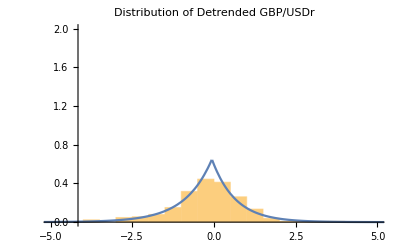

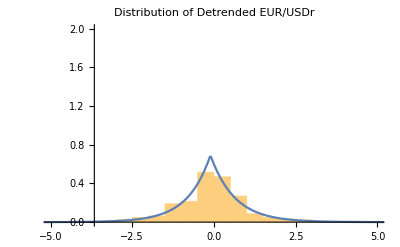

```mathematica
Show[Histogram[Subscript[L1, 1,1],Automatic,"ProbabilityDensity"],Plot[Subscript[F1, 1,1],{x,-10,10},PlotRange->{Full,Full}],PlotLabel->"Distribution of Detrended GBP/USDr",PlotRange->{{-5,5},{0,2}}]
Show[Histogram[Subscript[L2, 1,1],Automatic,"ProbabilityDensity"],Plot[Subscript[F2, 1,1],{x,-10,10},PlotRange->{Full,Full}],PlotLabel->"Distribution of Detrended EUR/USDr",PlotRange->{{-5,5},{0,2}}]
```

We estimate the detrended log return via student t copula by estimating the correlation matrix and degree of freedom.

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Subscript[R12, n,j]=Sin[Pi*KendallTau[Subscript[L1, n,j],Subscript[L2, n,j]]/2];
Subscript[R, n,j]={{1,Subscript[R12, n,j]},{Subscript[R12, n,j],1}}]]
```

```mathematica
For[n=1,n<9,n++,
For[j=1,j<11,j++,
Subscript[data, n,j]=Table[{Subscript[L1, n,j][[i]],Subscript[L2, n,j][[i]]},{i,1,252}]]]
```

```mathematica
n=1;
For[j=1,j<11,j++,
Print[EstimatedDistribution[Subscript[data, n,j],CopulaDistribution[{"MultivariateT",Subscript[R, n,j],Subscript[v, n,j]},{StudentTDistribution[Subscript[v, n,j]],StudentTDistribution[Subscript[v, n,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

CopulaDistribution[{MultivariateT,{{1,0.657205},{0.657205,1}},6.73466},{StudentTDistribution[6.73466],StudentTDistribution[6.73466]}]

CopulaDistribution[{MultivariateT,{{1,0.65713},{0.65713,1}},6.72648},{StudentTDistribution[6.72648],StudentTDistribution[6.72648]}]

CopulaDistribution[{MultivariateT,{{1,0.661537},{0.661537,1}},6.67731},{StudentTDistribution[6.67731],StudentTDistribution[6.67731]}]

CopulaDistribution[{MultivariateT,{{1,0.664437},{0.664437,1}},6.62195},{StudentTDistribution[6.62195],StudentTDistribution[6.62195]}]

CopulaDistribution[{MultivariateT,{{1,0.667771},{0.667771,1}},6.52203},{StudentTDistribution[6.52203],StudentTDistribution[6.52203]}]

CopulaDistribution[{MultivariateT,{{1,0.669101},{0.669101,1}},6.51144},{StudentTDistribution[6.51144],StudentTDistribution[6.51144]}]

CopulaDistribution[{MultivariateT,{{1,0.67271},{0.67271,1}},6.47868},{StudentTDistribution[6.47868],StudentTDistribution[6.47868]}]

CopulaDistribution[{MultivariateT,{{1,0.675938},{0.675938,1}},6.46668},{StudentTDistribution[6.46668],StudentTDistribution[6.46668]}]

CopulaDistribution[{MultivariateT,{{1,0.669544},{0.669544,1}},6.46272},{StudentTDistribution[6.46272],StudentTDistribution[6.46272]}]

CopulaDistribution[{MultivariateT,{{1,0.671386},{0.671386,1}},6.43979},{StudentTDistribution[6.43979],StudentTDistribution[6.43979]}]

```mathematica
Subscript[v, 1,1]=6.734658186746883;
Subscript[v, 1,2]=6.726478353071836;
Subscript[v, 1,3]=6.677310235102726;
Subscript[v, 1,4]=6.621945201819265;
Subscript[v, 1,5]=6.522026860128871;
Subscript[v, 1,6]=6.511443312037319;
Subscript[v, 1,7]=6.478680722468565;
Subscript[v, 1,8]=6.4666775536911985;
Subscript[v, 1,9]=6.462724684697369;
Subscript[v, 1,10]=6.439787773116503;
```

```mathematica
For[j=1,j<11,j++,
Print[EstimatedDistribution[Subscript[data, 7,j],CopulaDistribution[{"MultivariateT",Subscript[R, 7,j],Subscript[v, 7,j]},{StudentTDistribution[Subscript[v, 7,j]],StudentTDistribution[Subscript[v, 7,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

CopulaDistribution[{MultivariateT,{{1,0.512507},{0.512507,1}},20221.6},{StudentTDistribution[20221.6],StudentTDistribution[20221.6]}]

CopulaDistribution[{MultivariateT,{{1,0.504981},{0.504981,1}},170942.},{StudentTDistribution[170942.],StudentTDistribution[170942.]}]

CopulaDistribution[{MultivariateT,{{1,0.515234},{0.515234,1}},24961.},{StudentTDistribution[24961.],StudentTDistribution[24961.]}]

CopulaDistribution[{MultivariateT,{{1,0.512763},{0.512763,1}},9422.81},{StudentTDistribution[9422.81],StudentTDistribution[9422.81]}]

CopulaDistribution[{MultivariateT,{{1,0.516425},{0.516425,1}},4081.97},{StudentTDistribution[4081.97],StudentTDistribution[4081.97]}]

CopulaDistribution[{MultivariateT,{{1,0.519399},{0.519399,1}},66449.2},{StudentTDistribution[66449.2],StudentTDistribution[66449.2]}]

CopulaDistribution[{MultivariateT,{{1,0.518805},{0.518805,1}},4842.94},{StudentTDistribution[4842.94],StudentTDistribution[4842.94]}]

CopulaDistribution[{MultivariateT,{{1,0.517276},{0.517276,1}},78813.1},{StudentTDistribution[78813.1],StudentTDistribution[78813.1]}]

CopulaDistribution[{MultivariateT,{{1,0.523299},{0.523299,1}},429762.},{StudentTDistribution[429762.],StudentTDistribution[429762.]}]

CopulaDistribution[{MultivariateT,{{1,0.516255},{0.516255,1}},37570.9},{StudentTDistribution[37570.9],StudentTDistribution[37570.9]}]

```mathematica
Subscript[v, 7,1]=20221.563861573653;
Subscript[v, 7,2]=170941.83587101309;
Subscript[v, 7,3]=24961.008597255102;
Subscript[v, 7,4]=9422.814778443495;
Subscript[v, 7,5]=4081.9713612258133;
Subscript[v, 7,6]=66449.1840527003;
Subscript[v, 7,7]=4842.936482263042;
Subscript[v, 7,8]=78813.0899399507;
Subscript[v, 7,9]=429761.5255731024;
Subscript[v, 7,10]=37570.86509750521;
```

```mathematica
n=8;
For[j=1,j<11,j++,
Print[EstimatedDistribution[Subscript[data, n,j],CopulaDistribution[{"MultivariateT",Subscript[R, n,j],Subscript[v, n,j]},{StudentTDistribution[Subscript[v, n,j]],StudentTDistribution[Subscript[v, n,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

CopulaDistribution[{MultivariateT,{{1,0.511056},{0.511056,1}},45194.6},{StudentTDistribution[45194.6],StudentTDistribution[45194.6]}]

CopulaDistribution[{MultivariateT,{{1,0.511056},{0.511056,1}},15551.2},{StudentTDistribution[15551.2],StudentTDistribution[15551.2]}]

CopulaDistribution[{MultivariateT,{{1,0.504896},{0.504896,1}},39498.3},{StudentTDistribution[39498.3],StudentTDistribution[39498.3]}]

CopulaDistribution[{MultivariateT,{{1,0.513615},{0.513615,1}},15176.7},{StudentTDistribution[15176.7],StudentTDistribution[15176.7]}]

CopulaDistribution[{MultivariateT,{{1,0.50815},{0.50815,1}},9685.61},{StudentTDistribution[9685.61],StudentTDistribution[9685.61]}]

CopulaDistribution[{MultivariateT,{{1,0.50892},{0.50892,1}},682572.},{StudentTDistribution[682572.],StudentTDistribution[682572.]}]

CopulaDistribution[{MultivariateT,{{1,0.50738},{0.50738,1}},366411.},{StudentTDistribution[366411.],StudentTDistribution[366411.]}]

CopulaDistribution[{MultivariateT,{{1,0.504638},{0.504638,1}},56081.3},{StudentTDistribution[56081.3],StudentTDistribution[56081.3]}]

CopulaDistribution[{MultivariateT,{{1,0.500086},{0.500086,1}},28276.4},{StudentTDistribution[28276.4],StudentTDistribution[28276.4]}]

CopulaDistribution[{MultivariateT,{{1,0.503609},{0.503609,1}},120933.},{StudentTDistribution[120933.],StudentTDistribution[120933.]}]

```mathematica
Subscript[v, 8,1]=45194.64659864988;
Subscript[v, 8,2]=15551.180761611611;
Subscript[v, 8,3]=39498.31767287436;
Subscript[v, 8,4]=15176.684839340503;
Subscript[v, 8,5]=9685.61439568515;
Subscript[v, 8,6]=682572.3055826408;
Subscript[v, 8,7]=366410.61996660655;
Subscript[v, 8,8]=56081.26152596558;
Subscript[v, 8,9]=28276.36147687205;
Subscript[v, 8,10]=120933.47388826693;
```

The generate the 10 forecasts of each period. And compare with the actual data.

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],252];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],252];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],252];
For[i=1,i≤252,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,252}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,252}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

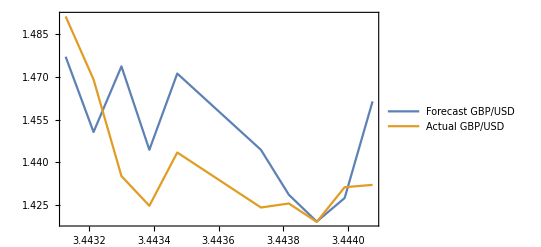

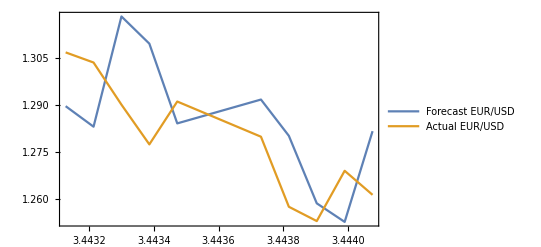

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,273+252*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,273+252*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,274+252*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]];
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[K1, n]*Subscript[b1, n,j,252]+Subscript[l1, n,j][[252]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[K2, n]*Subscript[b2, n,j,252]+Subscript[l2, n,j][[252]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,274+252*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,274+252*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

```mathematica
n=7;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],252];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],252];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],252];
For[i=1,i≤252,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,252}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,252}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

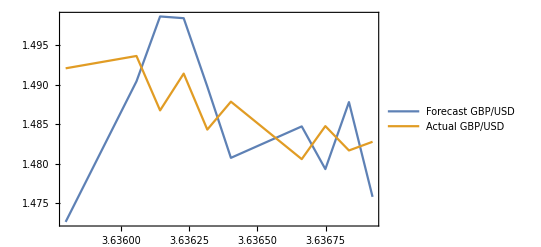

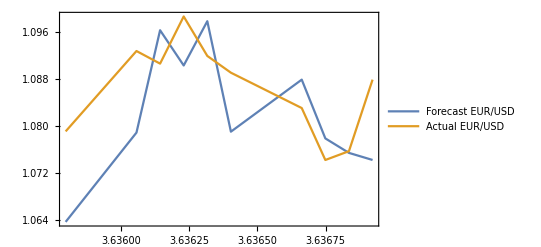

```mathematica
n=7;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,273+252*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,273+252*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,274+252*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]];
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[K1, n]*Subscript[b1, n,j,252]+Subscript[l1, n,j][[252]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[K2, n]*Subscript[b2, n,j,252]+Subscript[l2, n,j][[252]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,274+252*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,274+252*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

```mathematica
n=8;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],252];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],252];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],252];
For[i=1,i≤252,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,252}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,252}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

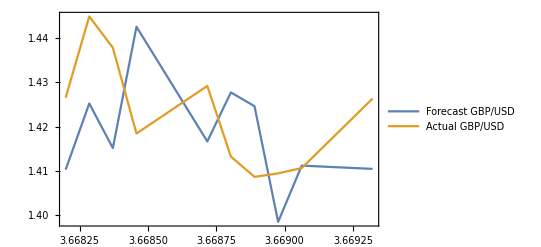

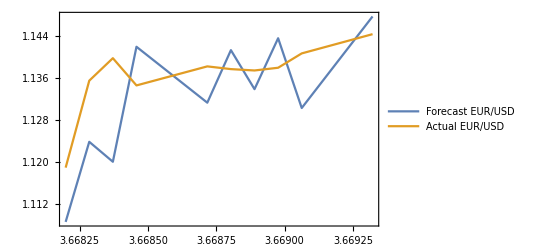

```mathematica
n=8;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,273+252*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,273+252*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,274+252*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]];
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[K1, n]*Subscript[b1, n,j,252]+Subscript[l1, n,j][[252]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[K2, n]*Subscript[b2, n,j,252]+Subscript[l2, n,j][[252]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,274+252*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,274+252*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

Use the random walk model to fit the data.

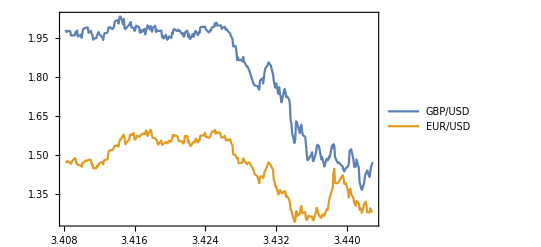

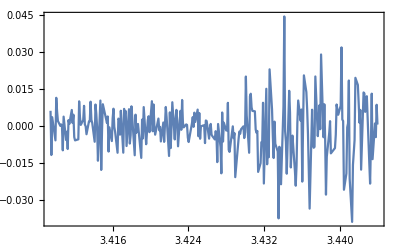

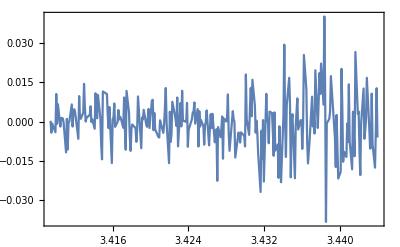

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,252*(n-1)+j-1],274];
Subscript[eurusd, n,j]=Take[Drop[eurusd,252*(n-1)+j-1],274];
Subscript[return1, n,j]=Take[Drop[gbpusdr,252*(n-1)+j-1],273];
Subscript[return2, n,j]=Take[Drop[eurusdr,252*(n-1)+j-1],273];
Subscript[GBPUSD, n,j]=Take[Drop[GBPUSD,252*(n-1)+j-1],274];
Subscript[EURUSD, n,j]=Take[Drop[EURUSD,252*(n-1)+j-1],274];
Subscript[Return1, n,j]=Take[Drop[GBPUSDr,252*(n-1)+j-1],273];
Subscript[Return2, n,j]=Take[Drop[EURUSDr,252*(n-1)+j-1],273]];
DateListPlot[{Subscript[GBPUSD, n,1],Subscript[EURUSD, n,1]},PlotLegends->Placed[{"GBP/USD","EUR/USD"},Above]]
DateListPlot[{Subscript[Return1, n,1]},PlotLegends->Placed["Daily Log Return of GBP/USD",Above]]
DateListPlot[{Subscript[Return2, n,1]},PlotLegends->Placed["Daily Log Return of EUR/USD",Above]]
```

```mathematica
AutocorrelationTest[Subscript[return1, 1,1],20,"TestConclusion"]
```

The null hypothesis that the data are uncorrelated to lag 20 is rejected at the 5 percent level based on the Ljung-Box test.

Plot the autocorrelation see the stationary of the log returns. Here, we didn’t plot all the LjungBoxPlot, but we have checked all the rolling windows.

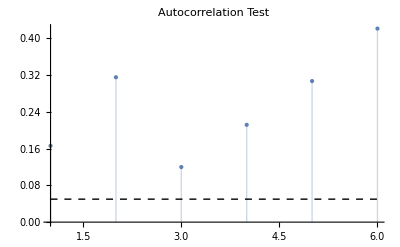

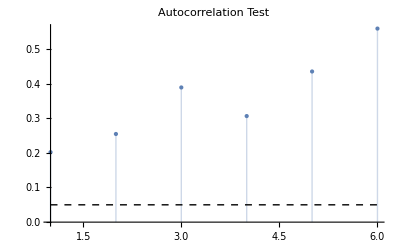

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,252*(n-1)+j-1],274];
Subscript[eurusd, n,j]=Take[Drop[eurusd,252*(n-1)+j-1],274];
Subscript[return1, n,j]=Take[Drop[gbpusdr,252*(n-1)+j-1],273];
Subscript[return2, n,j]=Take[Drop[eurusdr,252*(n-1)+j-1],273];
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}]];
Subscript[arima1, n,1]["LjungBoxPlot"]
Subscript[arima2, n,1]["LjungBoxPlot"]
```

Then we generate the 10 one-step ahead forecasts of the random walk for period 1, 7, 8.

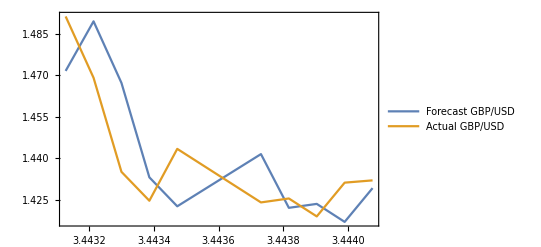

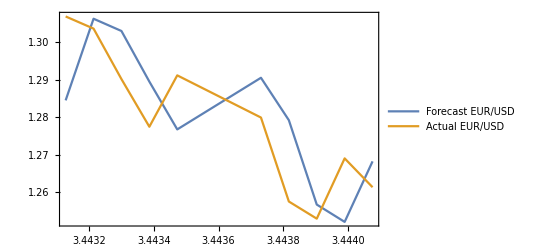

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,252*(n-1)+j-1],274];
Subscript[eurusd, n,j]=Take[Drop[eurusd,252*(n-1)+j-1],274];
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

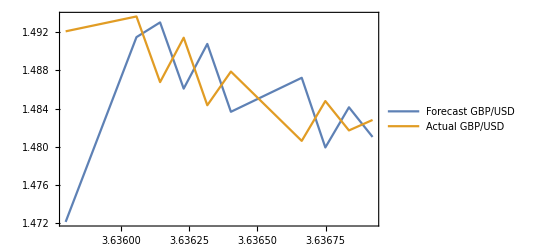

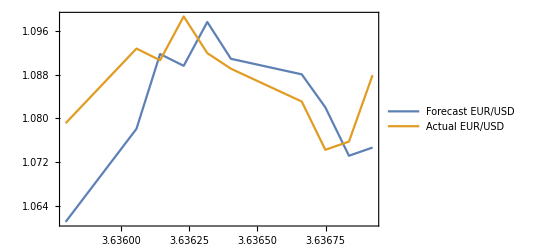

```mathematica
n=7;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,252*(n-1)+j-1],274];
Subscript[eurusd, n,j]=Take[Drop[eurusd,252*(n-1)+j-1],274];
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

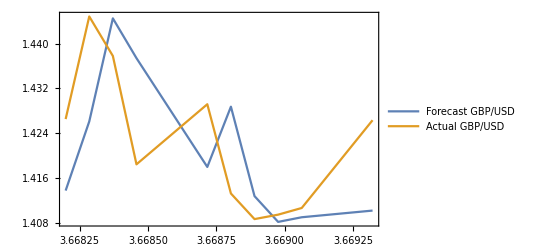

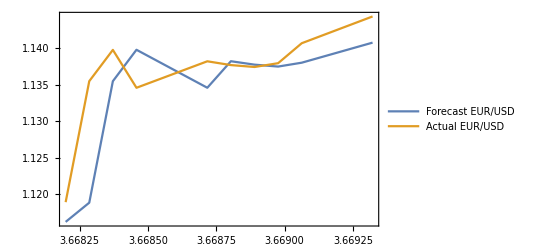

```mathematica
n=8;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,252*(n-1)+j-1],274];
Subscript[eurusd, n,j]=Take[Drop[eurusd,252*(n-1)+j-1],274];
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above],PlotRange->All]
```

Compare the forecasts of D&K model,  random walk model and actual data.

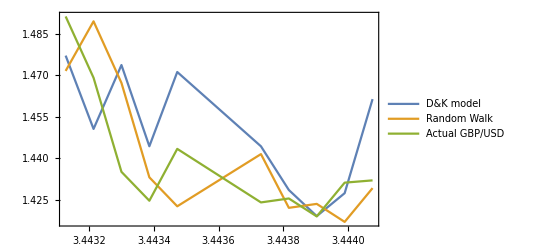

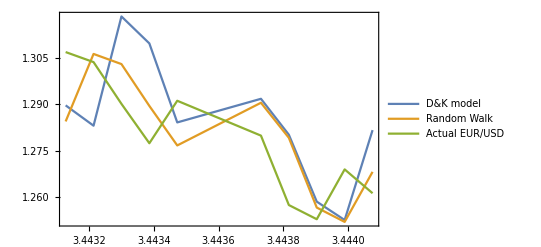

```mathematica
n=1;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

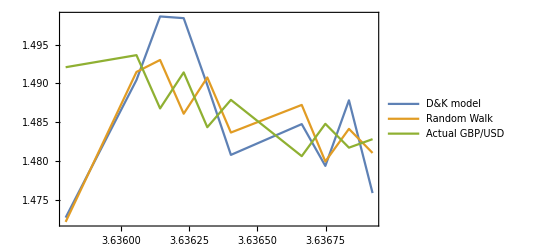

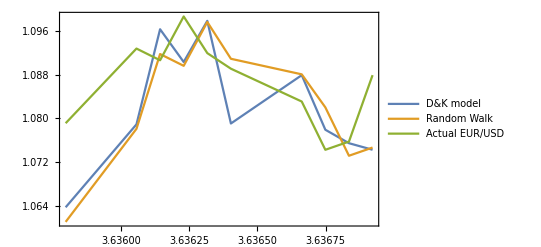

```mathematica
n=7;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

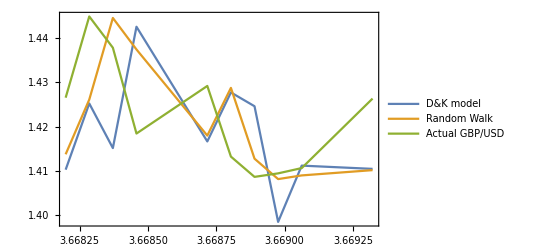

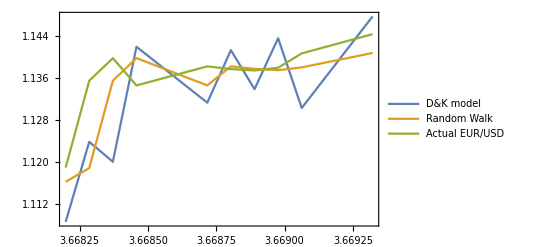

```mathematica
n=8;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

Compare the mean square error of different models and check the prediction power via DM test. Make sure the loss differential is weak stationary.

0.0004475

0.0293515

0.000287606

0.000195229

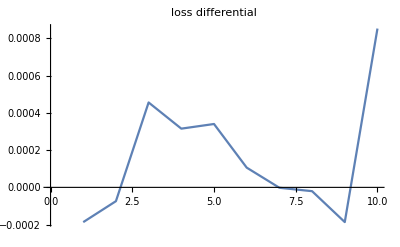

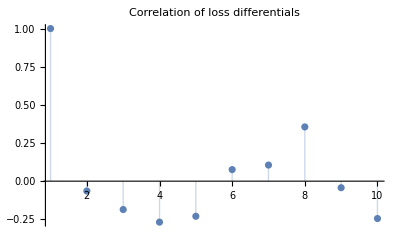

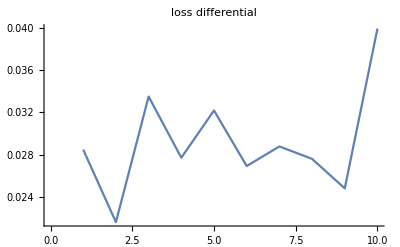

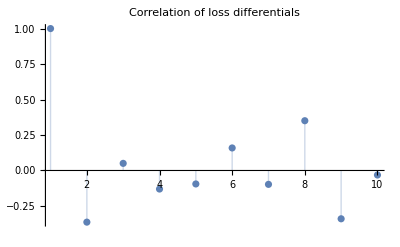

```mathematica
n=1;
Subscript[Predict1, n]=Take[Drop[gbpusd,274+252*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,274+252*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2](*mean square error of dk model of gbp*)
MSEdke=Mean[Subscript[forecasterror2, n]^2](*mean square error of dk model of eur*)
MSErwg=Mean[Subscript[earima1, n]^2](*mean square error of rw model of gbp*)
MSErwe=Mean[Subscript[earima2, n]^2](*mean square error of rw model of eur*)
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

0.0000790759

0.159679

0.0000607392

0.0000930027

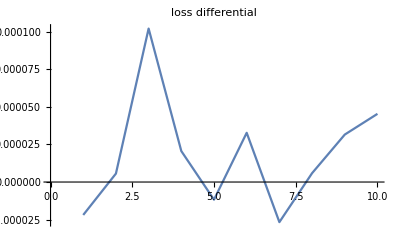

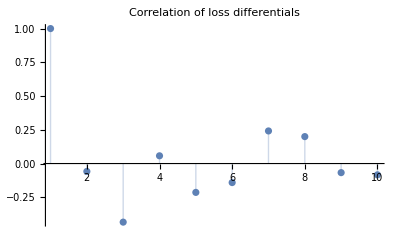

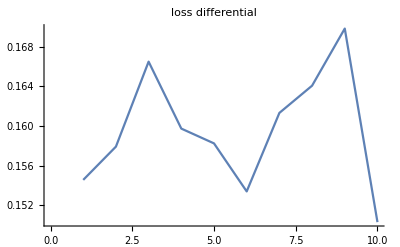

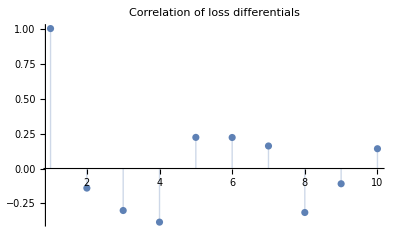

```mathematica
n=7;
Subscript[Predict1, n]=Take[Drop[gbpusd,274+252*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,274+252*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2]
MSEdke=Mean[Subscript[forecasterror2, n]^2]
MSErwg=Mean[Subscript[earima1, n]^2]
MSErwe=Mean[Subscript[earima2, n]^2]
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

0.000273957

0.0795666

0.000157035

0.0000361166

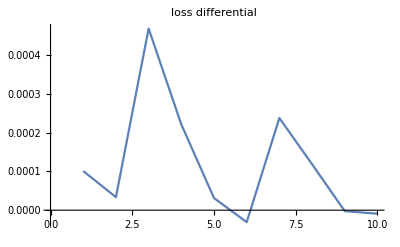

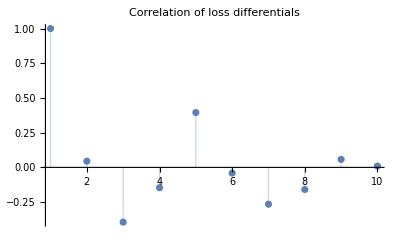

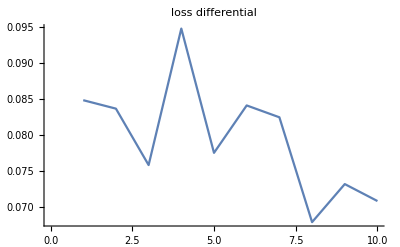

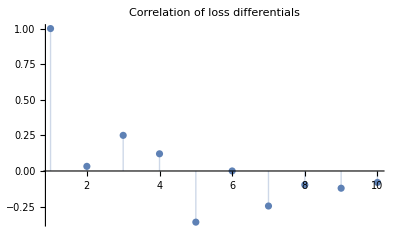

```mathematica
n=8;
Subscript[Predict1, n]=Take[Drop[gbpusd,274+252*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,274+252*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2]
MSEdke=Mean[Subscript[forecasterror2, n]^2]
MSErwg=Mean[Subscript[earima1, n]^2]
MSErwe=Mean[Subscript[earima2, n]^2]
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

```mathematica
n=1;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

-2.1064×10^-24

0.-1.38986×10^8 ⅈ

f1_n <=0, False

-1.19643×10^-21

0.-1.0634×10^9 ⅈ

f1_n <=0, False

```mathematica
n=7;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

-6.17109×10^-27

0.-2.94477×10^8 ⅈ

f1_n <=0, False

1.34809×10^-22

1.73398×10^10

{1.73398×10^10,False}

```mathematica
n=8;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

-8.22812×10^-26

0.-5.14227×10^8 ⅈ

f1_n <=0, False

3.50505×10^-21

1.69472×10^9

{1.69472×10^9,False}

Base on the difference of forecasts and actual data, we can see the direction of change of our forecasts.

```mathematica
n=1;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{0.00452113,-0.0232102,-0.0242285,-0.0148172,0.0161172,-0.000817134,-0.0131588,-0.0198534,0.0197095}

{-0.022126,-0.0339439,-0.0104277,0.0187136,-0.0193223,0.00142105,-0.00647319,0.0121859,0.000819836}

{0.00452113,-0.0232102,-0.0242285,-0.0148172,0.0161172,-0.000817134,-0.0131588,-0.0198534,0.0197095}

{-0.00323688,-0.0134549,-0.0126906,0.0136901,-0.0112375,-0.0223728,-0.00456945,0.0160597,-0.00768336}

{0.0178921,-0.0222184,-0.0340725,-0.0104587,0.0188374,-0.0193889,0.00142204,-0.0064983,0.0121852}

{-0.022126,-0.0339439,-0.0104277,0.0187136,-0.0193223,0.00142105,-0.00647319,0.0121859,0.000819836}

{0.0217462,-0.00326786,-0.0134835,-0.0127355,0.0137568,-0.0113032,-0.0224755,-0.00461926,0.0161291}

{-0.00323688,-0.0134549,-0.0126906,0.0136901,-0.0112375,-0.0223728,-0.00456945,0.0160597,-0.00768336}

```mathematica
n=7;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{0.0210493,0.0033153,-0.00706388,-0.00352661,0.000684689,0.00131309,0.0000232365,0.003984,-0.00834875}

{0.00156007,-0.00688421,0.00465654,-0.0070841,0.00353362,-0.00726974,0.00417691,-0.00308,0.00109853}

{0.0210493,0.0033153,-0.00706388,-0.00352661,0.000684689,0.00131309,0.0000232365,0.003984,-0.00834875}

{0.0136789,-0.00214527,0.00802816,-0.00671816,-0.00285413,-0.00601575,-0.00884235,0.00150226,0.012171}

{0.0193726,0.00154658,-0.00694512,0.00468691,-0.00711618,0.00356696,-0.00730655,0.00421254,-0.00311059}

{0.00156007,-0.00688421,0.00465654,-0.0070841,0.00353362,-0.00726974,0.00417691,-0.00308,0.00109853}

{0.0170571,0.0137011,-0.00216066,0.00803413,-0.00674416,-0.00284938,-0.00605022,-0.00886783,0.001505}

{0.0136789,-0.00214527,0.00802816,-0.00671816,-0.00285413,-0.00601575,-0.00884235,0.00150226,0.012171}

```mathematica
n=8;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{0.0302573,0.00939662,-0.00500899,-0.0109402,0.0189612,-0.0262066,-0.0158277,0.0163544,-0.00452362}

{0.0183444,-0.00706339,-0.0193748,0.0107442,-0.0159561,-0.00457871,0.000794164,0.00119293,0.0156939}

{0.0302573,0.00939662,-0.00500899,-0.0109402,0.0189612,-0.0262066,-0.0158277,0.0163544,-0.00452362}

{0.0165167,0.00427059,-0.00517237,0.00361571,-0.000517941,-0.000258794,0.000517705,0.0027257,0.00365465}

{0.0123541,0.0184351,-0.00711623,-0.0194493,0.0107731,-0.0159866,-0.00461031,0.00083011,0.00119297}

{0.0183444,-0.00706339,-0.0193748,0.0107442,-0.0159561,-0.00457871,0.000794164,0.00119293,0.0156939}

{0.00262229,0.0165848,0.00429144,-0.00518471,0.00362141,-0.000467585,-0.000260663,0.00052788,0.00273935}

{0.0165167,0.00427059,-0.00517237,0.00361571,-0.000517941,-0.000258794,0.000517705,0.0027257,0.00365465}